# Pretrained Deep Convolution Neural Network approach

```mathematica
LaunchKernels[2]
```

{KernelObject[1,local],KernelObject[2,local]}

```mathematica
trainData =  Import["/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/datasets/train.mx"];
```

```mathematica
emotionTypes = {"happy", "neutral","sad","angry","surprise"};
```

## Import test dataset

```mathematica
testData = Import["/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/datasets/test.mx"]
```

{-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,-Graphics-→happy,5911,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise}
 |  |  |  |

```mathematica
imageDim = ImageDimensions[testData[[1]][[1]]]
```

{48,48}

```mathematica
deenCNN = NetModel["Wolfram ImageIdentify Net for WL 11.1"]
```

NetChain[]

```mathematica
truncatedNetwork = Take[deenCNN, {1,-3}];
```

```mathematica
deepCNNInceptionV3 = NetInitialize @NetChain[{truncatedNetwork, LinearLayer[Length[emotionTypes]], SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",emotionTypes}]
]
```

NetChain[]

```mathematica
toPreserve ={ "TrainedNet",
	"BatchLossList",
    "RoundLossList",
	"ValidationLossList",
          "LossEvolutionPlot",
          "RMSGradientEvolutionPlot",
"RMSWeightEvolutionPlot"};
```

```mathematica
lossFunction = CrossEntropyLossLayer["Index"];
```

```mathematica
outputDirInception= "/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/models/InceptionV3";
```

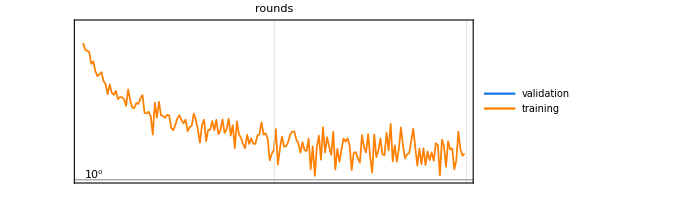
{NetChain[],{1.62367,1.67887,1.63294,1.67608,1.75571,1.66028,1.61457,1.42971,1.63332,1.61083,1.53761,1.64215,1.71415,1.57506,1.54443,1.57011,1.55223,1.50401,1.52409,1.54317,1.57559,1.50539,1.51228,1.58746,1.46869,1.50874,1.49988,1.4874,1.51173,1.48063,1.40864,1.45152,1.52537,1.46283,1.42068,1.48772,1.35847,1.47742,1.56549,1.53712,1.50826,1.3743,1.48963,1.3774,1.44472,1.3966,1.42652,1.41567,1.354,1.38949,1.39008,1.34387,1.46582,1.40961,1.35881,1.44433,1.324,1.42402,1.42617,1.33091,1.39195,1.35118,1.34051,1.3809,1.4268,1.43196,1.33583,1.3524,1.33052,1.31507,1.33081,1.40432,1.35197,1.30138,1.36577,1.40384,1.34132,1.31955,1.35354,1.40263,1.37268,1.33808,1.35131,1.31311,1.44922,1.20247,1.19619,1.40175,1.49388,1.27533,1.4072,1.40002,1.32831,1.3441,1.29192,1.39569,1.35343,1.22766,1.25388,1.3807,1.24209,1.3238,1.36846,1.27344,1.25671,1.38414,1.30897,1.3566,1.34942,1.39819,1.17724,1.36004,1.37479,1.38804,1.37815,1.26067,1.4191,1.30699,1.35324,1.38097,1.36302,1.3097,1.19235,1.24885,1.24484,1.32067,1.31504,1.22468,1.18167,1.368,1.31016,1.28023,1.17539,1.24368,1.32221,1.30845,1.06828,1.20173,1.23181,1.22068,1.27584,1.30221,1.31943,1.41209,1.29601,1.2581,1.21494,1.25466,1.35596,1.31776,1.27474,1.38009,1.28909,1.2759,1.22021,1.28861,1.38226,1.11385,1.18435,1.37758,1.35233,1.27245,1.10811,1.28945,1.23626,1.24367,1.24737,1.35242,1.31051,1.19549,1.33614,1.22561,1.21048,1.2519,1.11461,1.25998,1.16352,1.25976,1.27425,1.10418,1.14293,1.22466,1.29239,1.23509,1.34077,1.28064,1.05276,1.33891,1.29714,1.1779,1.15908,1.43744,1.36601,1.15776,1.17972,1.27809,1.26328,1.23442,1.22214,1.20149,1.15807,1.23117,1.32451,1.27779,1.23236,1.16037,1.21647,1.17367,1.15939,1.30106,1.16886,1.22644,1.25984,1.24221,1.15659,1.22028,1.3316,1.23334,1.42536,1.11019,1.23584,1.24287,1.36859,1.13911,1.13751,1.24759,1.15633,1.26778,1.098,1.182,1.17828,1.12687,1.15531,1.22213,1.27361,1.23865,1.26806,1.20791,1.18844,1.32418,1.11298,1.16122,1.21876,1.1161,1.26192,1.19823,1.20193,1.14594,1.30208,1.13928,1.14267,1.22289,1.30891,1.24691,1.28494,1.12342,1.19493,1.10914,1.27134,1.22338,1.28464,1.31434,1.26253,1.12625,1.13613,1.23326,1.20486,1.15402,1.13781,1.25763,1.14493,1.26146,1.13127,1.43124,1.23994,1.19316,1.13097,1.08323,1.32235,1.21505,1.17636,1.15586,1.30718,1.17605,1.39114,1.31804,1.06249,1.23535,1.12543,1.31728,1.26281,1.00025,1.11956,1.19346,1.23714,1.3396,1.30197,1.0075,1.11204,1.0711,1.13124,1.29532,1.33036,1.20208,1.11447,1.20236,1.31122,1.10252,1.15194,1.25042,1.08639,1.18076,1.20328,1.15281,1.1684,1.04071,1.06591,1.19036,1.11008,1.12572,1.25068,1.27679,1.11318,1.08174,1.23117,1.0558,1.16918,1.10711,1.247,1.03891,1.30887,1.06673,1.05742,1.19787,1.23532,1.07541,1.26364,1.07464,1.08794,1.13893,0.980007,1.19305,1.28126,1.25144,1.07342,1.41359,1.13386,1.11,1.34914,1.32007,0.993155,1.28209,1.23463,1.1687,1.02915,1.29029,1.19598,1.24376,1.1866,1.12078,1.12058,1.28344,1.01431,1.23616,1.05308,1.10844,1.0496,1.08609,1.06374,1.01762,1.25466,1.06296,1.07777,1.31007,1.02298,1.05225,1.27336,1.13957,1.27436,1.13411,1.05282,1.04987,1.0929,1.03599,1.11232,1.13173,0.982485,1.25897,1.23319,1.11976,1.10469,1.23268,1.13666,1.18302,1.1922,1.0053,1.10566,1.22069,1.04318,1.15486,1.18875,1.26889,1.03748,1.10268,1.21225,1.26284,1.11965,1.12995,1.11631,1.20038,1.18367,1.27403,1.18632,1.16934,1.25943,1.1644,1.05675,1.22674,1.13909,1.21408,1.06019,1.26501,1.15032,1.09666,1.28018,1.07241,1.01134,1.05601,1.2448,1.05808,1.04593,1.24593,1.09161,1.17303,1.17057,1.02858,1.12319,1.11205,1.13701,1.07467,1.18216,1.08189,1.20019,1.18975,0.992716,1.06638,1.12552,0.971872,1.15501,1.22612,1.15343,0.991499,1.0855,0.93321,1.07219,0.968311,1.09271,0.993991,1.18852,1.23612,1.0788,1.19614,1.15121,1.27944,1.182,1.10677,0.914195,1.1044,1.17263,1.11838,1.23679,1.32703,1.10354,1.04015,1.2157,1.06367,1.13206,1.26494,1.1892,1.09216,1.07724,1.2288,1.08399,1.13146,1.26949,0.936796,1.03568,1.14132,1.03693,1.29155,1.19435,1.25217,1.06559,1.14391,0.895855,1.04813,1.03143,1.10465,1.28786,1.06004,0.95215,0.950785,1.26173,1.10686,1.12498,1.17291,1.15183,1.01303,1.14342,1.15888,1.22889,1.12523,1.14101,0.96775,1.41192,1.08043,1.27402,1.01709,1.11345,1.25604,1.13643,1.11974,1.17544,1.10129,1.05193,1.06445,1.08343,0.946756,1.18059,1.09825,1.12744,1.01392,1.15297,1.15871,1.09901,1.01702,1.11516,1.16926,0.941563,1.10522,0.937795,1.07282,1.0618,1.18686,1.24818,1.05386,1.18189,1.23286,1.19408,0.963953,1.1364,1.21823,1.02152,1.1248,1.23664,1.04219,1.19288,1.23546,1.09839,1.20368,1.06746,1.05729,1.12911,1.10076,1.11974,0.912239,1.05353,1.02129,1.20086,1.213,1.21664,1.09564,1.08211,0.961486,1.18558,1.11846,1.08842,1.2038,1.16068,0.997417,1.29178,1.20295,0.968306,1.19548,1.02377,1.00053,1.2047,1.16329,1.11786,1.12105,1.20046,0.940436,1.04075,1.1945,1.29136,1.22787,1.2388,0.972463,0.965002,1.28124,1.09586,1.247,1.38394,1.18779,1.00571,0.971947,1.12865,1.17159,1.1606,1.29055,1.09477,0.995393,1.01878,1.01463,1.10429,1.13909,1.04517,1.18851,1.171,1.08141,1.31951,1.15227,1.12676,1.25129,1.1421,1.08437,1.15386,1.15554,1.08991,1.12319,0.995806,1.11969,1.1735,1.04267,1.07724,1.10313,1.015,1.19088,1.17089,1.03274,1.17867,1.11124,1.17553,1.14566,1.17778,1.14107,1.25334,1.25345,1.04212,1.08819,1.28488,1.08678,1.10657,0.936629,1.06724,1.10465,1.09078,1.21336,1.1219,1.06194,1.05049,1.04692,1.17199,0.967001,1.09443,1.17058,1.07733,1.15065,0.956833,1.07883,1.07488,1.11254,1.04213,1.22737,1.05995,1.10983,1.1776,1.00424,1.09575,1.02013,0.983707,1.04896,1.11643,1.27757,1.01114,1.03957,1.06106,1.17745,1.01022,1.34226,1.08127,1.1417,1.10033,1.16404,1.19663,1.08567,1.00329,0.948994,0.984657,1.12717,0.966057,1.12407,1.23253,1.3121,0.989946,1.19105,1.1279,1.21255,1.09404,0.915351,1.14651,1.04108,1.147,1.13394,1.1674,1.16087,1.12903,1.14625,1.24005,0.958508,1.15685,1.09276,1.15553,1.08762,0.992189,1.14165,0.955185,1.06942,0.985511,1.12974,0.931052,1.24893,1.01049,1.41195,1.17027,1.18144,0.980545,1.06681,1.18063,1.24978,1.04212,1.25927,1.15803,0.912772,0.973569,1.21112,1.04546,1.17396,1.3461,1.20957,1.09216},{1.27833,1.12141},{{376,1.85154}},-Graphics-,-Graphics-,-Graphics-}

```mathematica
trainedDeepCNNInceptionV3=NetTrain[deepCNNInceptionV3,trainData, lossFunction,toPreserve,MaxTrainingRounds-> 3,
TrainingProgressCheckpointing->{"Directory",outputDirInception},
Method->{"ADAM"},
ValidationSet->testData,
LearningRateMultipliers->{-2->1 ,_->None},
BatchSize->64
]
```

```mathematica
Export["/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/models/InceptionV3/transferLearinig.wlnet",trainedDeepCNNInceptionV3[[1]]]
```

/Users/adendek/Documents/Wolfram Mathematica/Intern/project/DeepLaetitia/scripts/smileDetector/models/InceptionV3/transferLearinig.wlnet

```mathematica
Dynamic[image=CurrentImage[];
box =  FindFaces[image];
face =   ImageTrim[image,#]&/@ box ;
face = face[[1]];
greyFace = ColorConvert[face,"Grayscale"];
Column[{image,greyFace,Column[trainedDeepCNNInceptionV3[[1]][greyFace,"TopProbabilities"]]}]]
```